# Quantum Systems Engineering, by Computing

A Wolfram Language / QuantumFramework companion to the Quantum Systems Engineering unit.

This document walks the entire arc of the unit, from Schrödinger's equation to quantum sensing, but it teaches every idea by building it as a computation you can run, modify, and break. The course is delivered in Python (Qiskit and QuTiP); here we do the same physics in the Wolfram QuantumFramework. The conviction is Feynman-flavored: if we cannot compute it, we have not really understood it. So every claim below is immediately followed by a cell that demonstrates or verifies it, and every number you see was produced by running the code, not asserted from a formula sheet.

We start where the course starts, with a particle trapped in a box, and use it to motivate the jump from messy calculus to clean linear algebra. We then build the engineer's two workhorses, the qubit and the quantum harmonic oscillator, drive them with fields, and watch them flop. We scale up to many qubits, gates, and circuits; send a state across a channel by teleportation; open the system to its environment and watch coherence decay; and finally turn that same fragility into a precision sensor. Four of these sections correspond directly to the four Python labs in the unit, and they are flagged as such.

A practical note on how to read this. Evaluate the cells top to bottom, as if this were one long laboratory session. Each section is self-contained enough to start from, but variables defined earlier are reused. Change the numbers. Detune the drive, raise the noise, add a qubit. The framework will tell you what happens.

## Setup

Everything below uses one paclet plus its second-quantization sub-package. Load both up front. The sub-package carries the oscillator and quantum-optics tools (AnnihilationOperator, FockState, CoherentState, the quadrature operators, OperatorVariance, G2Coherence); a bare Needs of the main context leaves these inert, so we load it now even though it is first needed in Part 5.

```mathematica
Needs["Wolfram`QuantumFramework`"]
Needs["Wolfram`QuantumFramework`SecondQuantization`"]
```

The three central objects are QuantumState (a ket or a density matrix), QuantumOperator (a matrix that acts on states, including Hamiltonians and gates), and QuantumCircuitOperator (an ordered list of operations). Each is a property-carrying object: you ask it questions with object["Property"] rather than calling dozens of separate functions. That is the single most important habit to build here. When you want the Bloch vector, the purity, whether an operator is Hermitian, or a variance, ask the object: qs["BlochVector"], qs["Purity"], op["HermitianQ"], OperatorVariance[qs, op]. We reach for raw matrices only to build an operator, never to interrogate one. We will lean on that pattern constantly.

## Part 1 — From wave mechanics to a finite Hilbert space (Lab 1)

Course map: Weeks 1 and 3. This is Lab 1 (particle in a box, finite/infinite well).

The course opens with Schrödinger's equation and the infinite square well because it is the simplest place where energy quantization falls out of a boundary condition. A particle of mass m confined to 0≤x≤L with infinite walls has stationary states ψ_n(x)=√(2/L) sin (nπx/L) and energies E_n=n^2 π^2 ℏ^2/(2m L^2). The physics worth keeping is the scaling: the n-th level sits at n^2 times the ground energy.

We do not discretize this by hand. The Wolfram Language has a native quantum operator for exactly this problem: SchrodingerPDEComponent assembles the differential operator -ℏ^2/(2m)∇^2 +V(x) from physical parameters, and NDEigensystem finds its eigenvalues and eigenstates under the boundary conditions we impose. The infinite walls are a DirichletCondition forcing ψ=0 at the edges of the box. Set ℏ=m=1, V=0 inside, and solve on [0,1]:

```mathematica
Hbox = SchrodingerPDEComponent[{ψ[x], {x}},
   <|"Mass" -> 1, "ReducedPlanckConstant" -> 1, "SchrodingerPotential" -> 0|>];
{energies, modes} = NDEigensystem[
   {Hbox, DirichletCondition[ψ[x] == 0, True]}, ψ[x], {x, 0, 1}, 5];
energies
```

{4.93481,19.7395,44.4162,78.9736,123.433}

This returns {4.93, 19.74, 44.42, 78.97, 123.43}, matching the exact E_k=k^2 π^2/(2 L^2)={4.93, 19.74, 44.41, 78.96, 123.37} to better than a part in a thousand, with no hand-built matrix anywhere.

The clean physical statement is the ratio. Verify that the levels scale as k^2:

```mathematica
energies/First[energies]
```

{1.,4.00005,9.0006,16.0034,25.0128}

The result {1., 4.00, 9.00, 16.00, 25.01} is {1, 4,9,16, 25}. The boundary condition alone forces the k^2 ladder.

Each eigenstate is a continuous wavefunction. To bring it into QuantumFramework, which works in finite-dimensional Hilbert spaces, sample it on a grid and hand the values to a QuantumState, which normalizes them into a unit vector:

```mathematica
grid = Subdivide[0., 1., 64];
ground = QuantumState[(modes[[1]] /. x -> #) & /@ grid]["Normalize"];
ground["Norm"]
```

1.

ground["Norm"] is 1.: a genuine normalized state, its amplitudes the half-sine sin (πx/L) peaked at the center of the box.

This is the bridge for the whole unit. A continuous wave-mechanics problem was solved natively, and its ground state became a QuantumState. From here on we work in finite-dimensional Hilbert spaces, where the language is pure linear algebra. (The finite-well version, where the walls are a finite barrier, is Lab 1 at the end.)

## Part 2 — States, observables, and measurement

Course map: Weeks 2 and 3 (Dirac notation, Hilbert space, observables, the statistical interpretation, uncertainty).

A pure quantum state is a unit vector. The smallest interesting case is the qubit, a two-level system. In Dirac notation we write kets like 0 and 1 for the computational basis and +=(0+1)/√2 for an equal superposition. Build a few and look at one:

```mathematica
zero = QuantumState["0"]; one = QuantumState["1"]; plus = QuantumState["+"];
psi = QuantumState[{1, I}/Sqrt[2]];
psi["StateVector"] // Normal
```

{1/(√2),ⅈ/(√2)}

This returns {1/√2,  i/√2}. The state psi is (0+i1)/√2, and psi["Norm"] is 1.

The bra ψ is the conjugate-transpose of the ket, obtained with the "Dagger" property. The inner product ϕψ is then a bra applied to a ket, and its numerical value is the "Scalar" of the resulting zero-qudit object. Compute 0+:

```mathematica
(zero["Dagger"] @ plus)["Scalar"]
```

1/(√2)

The answer is 1/√2, the overlap of 0 with +. This single idiom, (bra["Dagger"] @ ket)["Scalar"], is how we extract every amplitude, overlap, and expectation value below.

An observable is a Hermitian operator. The Pauli operators X, Y, Z are the basic qubit observables. Look at Z and confirm it is Hermitian with real eigenvalues ±1:

```mathematica
Z = QuantumOperator["Z"];
{Z["HermitianQ"], Z["Eigenvalues"]}
```

{True,{-1,1}}

This returns {True, {-1, 1}}: we ask the operator whether it is Hermitian rather than pulling out its matrix and testing by hand. The eigenvalues are the possible measurement outcomes; the eigenvectors 0, 1 are the states that yield those outcomes with certainty. Hermiticity is exactly the guarantee that the outcomes are real.

The expectation value ψAψ is the mean outcome of measuring A in state ψ. There are several equivalent ways to compute it, and seeing them agree builds confidence. Compute ⟨+|Z|+⟩ three ways, by a trace, by a bra-operator-ket sandwich, and by an explicit measurement:

```mathematica
{
  Tr[Z["Matrix"] . plus["DensityMatrix"]],
  (plus["Dagger"] @ Z @ plus)["Scalar"],
  QuantumMeasurementOperator[Z][plus]["Mean"]
} // Chop
```

{0,0,0}

All three return 0. In the state +, Z is equally likely to give +1 or -1, so its mean is zero.

Measurement is more than its mean: it is a probability distribution over eigenvalues. Apply a Z measurement to + and read the outcome probabilities:

```mathematica
qm = QuantumMeasurementOperator["Z"][plus];
Values[qm["Probabilities"]]
```

{1/2,1/2}

The result is {1/2, 1/2}. This is the Born rule in action: the probability of an outcome is the squared overlap of the state with the corresponding eigenvector.

The uncertainty principle quantifies how unsharp two incompatible observables must be. The Robertson relation says ΔAΔB≥1/2|⟨[A, B]⟩|, where ΔA=√(⟨A^2⟩-⟨A⟩^2). We do not hand-roll the variance: OperatorVariance[state, op] is exactly ⟨O^2⟩-⟨O⟩^2, and Commutator[A, B] is the built-in AB-BA. Check the relation for X and Y on a generic complex state, one tilted off all three axes so the bound actually bites:

```mathematica
st = QuantumState[{Cos[Pi/8], Exp[I Pi/5] Sin[Pi/8]}];
X = QuantumOperator["X"]; Y = QuantumOperator["Y"];
{Sqrt[OperatorVariance[st, X] OperatorVariance[st, Y]],
 Abs[(st["Dagger"] @ Commutator[X, Y] @ st)["Scalar"]]/2} // N // Chop
```

{0.746011,0.707107}

This returns {0.746, 0.707}: the product of spreads exceeds the bound 1/2|⟨[X, Y]⟩|=|⟨Z⟩|, and the inequality is strict. For a pure qubit state the exact relation is Δ X^2 Δ Y^2=⟨Z⟩^2+⟨X⟩^2⟨Y⟩^2, so the bound is reached only when one of ⟨X⟩, ⟨Y⟩ vanishes. Here neither does, so the state cannot even saturate the limit. The inequality is never violated, which is the whole content of the uncertainty principle: you cannot make both spreads small when the observables fail to commute. (Part 5 will show the oscillator's ground state hitting the bound exactly.)

Before moving on, the key results so far, all computed:

A pure qubit state is a unit vector; the bra is its conjugate transpose, obtained with "Dagger".

Inner products, amplitudes, and expectation values all reduce to (bra @ ket)["Scalar"].

Observables are Hermitian operators; their eigenvalues are the outcomes and are real.

Measurement returns a Born-rule probability distribution, not just a number.

Non-commuting observables obey the Robertson uncertainty bound.

## Part 3 — Dynamics and the three pictures

Course map: Week 3 (postulates; Schrödinger, Heisenberg, and interaction pictures).

A closed quantum system evolves by the Schrödinger equation i∂_t ψ=Hψ, whose solution is ψ(t)=e^-iHt ψ(0). QuantumEvolve solves this for us. Called with no time range, it returns a closed-form symbolic state, which is the cleanest thing to learn from. Evolve + under H=Z (free precession of a spin in a field along z):

```mathematica
sol = QuantumEvolve[QuantumOperator["Z"], QuantumState["+"]];
sol["StateVector"] // Normal // Simplify
```

{ⅇ^(-ⅈ t)/(√2),ⅇ^(ⅈ t)/(√2)}

The result is {e^-it/√2,  e^it/√2}, with the framework using a formal time symbol. The two amplitudes acquire opposite phases, so the state rotates around the z-axis of the Bloch sphere at angular frequency 2. This is Larmor precession, derived with one line.

When a closed form is unavailable or unwanted, give QuantumEvolve a numeric time range and it integrates the equation, returning a state you sample at any time with sol[<|t -> value|>]. We use that form in the next two parts.

The three pictures are three bookkeeping conventions for the same physics. In the Schrödinger picture the state moves and operators are fixed. In the Heisenberg picture the state is fixed and operators move as A(t)=e^iHt A e^-iHt. Expectation values, the only measurable quantities, are identical in both. QuantumEvolve handles either: pass it a state and it moves the state; pass it an observable (with an empty Lindblad list {}) and it returns the Heisenberg-evolved operator. Compute ⟨X(t)⟩ under H=Z both ways:

```mathematica
H = QuantumOperator["Z"];
schrod = QuantumEvolve[H, QuantumState["+"]];
xSchrodinger = (schrod["Dagger"] @ QuantumOperator["X"] @ schrod)["Scalar"] // ComplexExpand // Simplify;
Xt = QuantumEvolve[H, {}, QuantumOperator["X"]];
xHeisenberg = (QuantumState["+"]["Dagger"] @ Xt @ QuantumState["+"])["Scalar"] // ComplexExpand // Simplify;
{xSchrodinger, xHeisenberg}
```

{Cos[2 t],Cos[2 t]}

Both return cos (2t): the expectation of X oscillates as the state precesses, and the Schrödinger and Heisenberg computations agree identically. The interaction picture, introduced next for the driven qubit, is the same idea applied to the part of H we already understand, leaving only the interesting interaction in the equations.

## Part 4 — The qubit and Rabi flopping (Lab 2)

Course map: Week 4 (two-level system driven by classical radiation, Pauli matrices, interaction picture, Rabi flopping, Bloch sphere). This is Lab 2.

A two-level atom driven by a resonant classical field, viewed in the interaction picture, has the simple Hamiltonian H=(Ω/2) X, where Ω is the Rabi frequency set by the drive strength. Starting in the ground state 0, the population sloshes coherently to the excited state and back. Evolve symbolically and read the amplitudes:

```mathematica
Ω = 1;
Hdrive = (Ω/2) QuantumOperator["X"];
rabi = QuantumEvolve[Hdrive, QuantumState["0"]];
rabi["StateVector"] // Normal // Simplify
```

{Cos[t/2],-ⅈ Sin[t/2]}

The state is {cos (t/2),  -isin (t/2)} (with Ω=1). The excited-state probability is therefore P_1(t)=sin^2 (Ωt/2): complete, periodic population transfer. A pulse of duration t=π/Ω is a π-pulse, which flips 0 to 1; a pulse of half that is a π/2-pulse, which builds an equal superposition. These are the elementary control operations of every qubit platform.

Real drives are never perfectly on resonance. With a detuning δ between the drive and the qubit, the interaction-picture Hamiltonian gains a z-term: H=(Ω/2)X+(δ/2)Z. Evolve and extract the excited-state probability as a function of time and detuning:

```mathematica
Hdet = (1/2) QuantumOperator["X"] + (δ/2) QuantumOperator["Z"];
rabiDet = QuantumEvolve[Hdet, QuantumState["0"]];
sv = rabiDet["StateVector"] // Normal;
FullSimplify[Abs[sv[[2]]]^2, Assumptions -> {δ ∈ Reals, t ∈ Reals}]
```

(Sin[1/2 t √(1+δ^2)]^2)/(1+δ^2)

The framework returns

P_1(t)=(sin^2 (t/2 √(1+δ^2)))/(1+δ^2),

which (with Ω=1, so δ is measured in units of Ω) is exactly the textbook detuned Rabi formula P_1=Ω^2/Ω_R^2 sin^2 (Ω_R t/2) with generalized Rabi frequency Ω_R=√(Ω^2+δ^2). Two things are visible at a glance: detuning speeds up the oscillation (Ω_R>Ω) and caps its amplitude below 1 (P_1^max=1/(1+δ^2)). You can no longer fully invert the qubit once you are off resonance.

The natural picture for a qubit is the Bloch sphere, where a pure state is a point on a unit sphere and a mixed state lies inside it. The Bloch vector is ⟨X⟩, ⟨Y⟩, ⟨Z⟩. Read it for a state at polar angle π/3:

```mathematica
QuantumState[{Cos[Pi/6], Sin[Pi/6]}]["BlochVector"]
```

{(√3)/2,0,1/2}

The result is {√3/2,  0,  1/2}, a unit vector tilted 60^∘ from the north pole. The framework will also draw it for you with QuantumState[{Cos[Pi/6], Sin[Pi/6]}]["BlochPlot"]. Under the resonant drive of this section, this arrow simply rotates about the X-axis; Rabi flopping is that rotation, seen in the populations.

## Part 5 — The quantum harmonic oscillator

Course map: Week 5 (classical analogy, operator method, number states, quantised light, Jaynes-Cummings interaction). Uses the second-quantization sub-package loaded in Setup.

The harmonic oscillator is the other system every quantum engineer must own, because it models a mode of the electromagnetic field in a cavity and a mechanical resonator alike. Its algebra is built from the lowering operator a and raising operator a^†, with [a, a^†]=1. In a truncated Fock space of size N, AnnihilationOperator[N] is the matrix with √k on the first super-diagonal:

```mathematica
a = AnnihilationOperator[5];
a["Matrix"] // Normal
```

{{0,1,0,0,0},{0,0,√2,0,0},{0,0,0,√3,0},{0,0,0,0,2},{0,0,0,0,0}}

The number operator n̂=a^†a counts excitations, and its diagonal is 0,1,2, …:

```mathematica
Diagonal[Normal[(a["Dagger"] @ a)["Matrix"]]]
```

{0,1,2,3,4}

This returns {0, 1, 2, 3, 4}. The eigenstates of n̂ are the number (Fock) states n, the energy eigenstates of the oscillator. FockState[2, 5] is 2 in a five-level truncation:

```mathematica
FockState[2, 5]["StateVector"] // Normal
```

{0,0,1,0,0}

which is {0, 0,1,0, 0}, a single excitation count with definite energy.

A coherent state α is the closest a quantum oscillator comes to a classical sinusoid: a displaced ground state with a Poisson distribution of photon numbers and mean occupation (|α|)^2. In the framework it is built parametrically in a formal amplitude; substitute a value to make it concrete:

```mathematica
coh = CoherentState[8][<|α -> 1.0|>];
a8 = AnnihilationOperator[8];
(coh["Dagger"] @ (a8["Dagger"] @ a8) @ coh)["Scalar"]
```

0.999927

The mean photon number comes out as 1.0, that is (|α|)^2 with α=1, confirming the Poisson mean.

Whether light is classical or nonclassical is decided by photon statistics, not by mean intensity. The second-order coherence g^(2)(0)=⟨a^†a^†aa⟩/⟨a^†a⟩^2 measures how photons bunch: a coherent (laser-like) field has g^(2)(0)=1, while a single-photon state has g^(2)(0)=0, since one photon cannot be detected twice at once. G2Coherence computes it from the state:

```mathematica
{G2Coherence[CoherentState[10][<|α -> 1.0|>]], G2Coherence[FockState[1, 10]]}
```

{0.999992,0}

The result is {1.0, 0}: the coherent state sits exactly at the classical boundary, and the single photon is perfectly antibunched. Any g^(2)(0)<1 is impossible for classical light and is the experimental signature of a true quantum emitter.

The oscillator is also where the position-momentum uncertainty lives. The quadratures X=(a+a^†)/2 and P=-i(a-a^†)/2 are the oscillator's "position" and "momentum"; in this normalization [X, P]=i/2. The ground state is a minimum-uncertainty state. Using the same OperatorVariance as in Part 2, verify that it saturates the bound:

```mathematica
{Xq, Pq} = QuadratureOperators[6];
gs = FockState[0, 6];
{OperatorVariance[gs, Xq], OperatorVariance[gs, Pq],
 OperatorVariance[gs, Xq] OperatorVariance[gs, Pq]}
```

{1/4,1/4,1/16}

This gives Δ X^2=Δ P^2=1/4 and a product 1/16, so ΔXΔP=1/4=1/2|⟨[X, P]⟩|. The vacuum is as sharp as quantum mechanics allows in both quadratures at once, the saturated case the strict qubit inequality of Part 2 anticipated.

Finally, the Jaynes-Cummings model couples one qubit to one field mode, the elementary model of light-matter interaction in a cavity (the extended topic of Week 5). On resonance and in the interaction picture, the coupling is H=g(σ^+a+σ^-a^†), where σ^± raise and lower the qubit and a, a^† destroy and create photons. Build it on a qubit-times-field space and watch a single excitation oscillate between atom and cavity:

```mathematica
nF = 4; g = 1;
σp = AnnihilationOperator[2]["Dagger"]; σm = AnnihilationOperator[2];
af = AnnihilationOperator[nF];
Hjc = g (QuantumTensorProduct[σp, af] + QuantumTensorProduct[σm, af["Dagger"]]);
psi0 = QuantumTensorProduct[QuantumState["1"], FockState[0, nF]];
jc = QuantumEvolve[Hjc, psi0, {t, 0, Pi}];
pe[tt_] := QuantumPartialTrace[jc[<|t -> tt|>], {2}]["ProbabilitiesList"][[2]] // Chop;
{pe[0], pe[Pi/4.], pe[Pi/2.]}
```

{1.,0.5,0}

The excited-state population is {1., 0.5, 0.}, matching P_e(t)=cos^2 (gt): the atom starts excited with the cavity empty (e, 0), and the energy quantum coherently shuttles to the field (g, 1) and back. This vacuum Rabi oscillation has no classical analog. The coupling term σ^+a+σ^-a^† links e, 0 directly to g, 1, so even with zero photons in the cavity the initial state is not an eigenstate of H and is forced to evolve. A classical field of zero amplitude would leave the atom alone; the quantized field does not.

## Part 6 — Many qubits: tensor products, gates, circuits

Course map: Week 6 (tensor product, multiple qubits, quantum gates, quantum circuits).

Two qubits live in the tensor product of their spaces, a four-dimensional Hilbert space. QuantumTensorProduct builds composite states and operators:

```mathematica
q00 = QuantumTensorProduct[QuantumState["0"], QuantumState["0"]];
{q00["Qudits"], q00["StateVector"] // Normal}
```

{2,{1,0,0,0}}

This reports 2 qudits and the vector {1, 0,0, 0}, that is 00. The dimension doubles with every qubit added, which is precisely the resource that makes quantum computers powerful and classical simulation hard.

A quantum circuit is an ordered list of gates acting on named wires. A gate is a unitary QuantumOperator; the basic library includes the Hadamard "H", the Paulis, phase gates, and the controlled-NOT "CNOT". Unitarity is what makes gates reversible, and we check it the object-model way:

```mathematica
{QuantumOperator["H"]["UnitaryQ"], QuantumOperator["CNOT"]["UnitaryQ"]}
```

{True,True}

Both are True. The canonical two-qubit circuit prepares a Bell pair: a Hadamard on the first wire followed by a CNOT controlled on it:

```mathematica
bell = QuantumCircuitOperator[{"H" -> 1, "CNOT" -> {1, 2}}];
bell[QuantumState["00"]]["StateVector"] // Normal
```

{1/(√2),0,0,1/(√2)}

The output is {1/√2, 0,0, 1/√2}, the entangled state Φ^+=(00+11)/√2. The notation "gate" -> wires reads like a wiring diagram, and bell["Diagram"] draws the actual circuit.

Circuits compose and scale. The three-qubit GHZ state, a maximally entangled "cat" state, is one more CNOT:

```mathematica
QuantumState["GHZ"[3]]["StateVector"] // Normal
```

{1/(√2),0,0,0,0,0,0,1/(√2)}

which is {1/√2, 0,0,0,0,0,0, 1/√2}, the state (000+111)/√2. Gates and circuits are the hardware-independent logical layer of quantum computing: the same bell circuit runs on any platform, exactly as the course frames it.

## Part 7 — Communication: entanglement, no-cloning, teleportation (Lab 3)

Course map: Week 8 (entanglement, Bell states, no-cloning, teleportation). This is Lab 3.

Quantum communication rests on entanglement, correlation stronger than anything classical. The Bell state Φ^+ is entangled, and the framework can certify it:

```mathematica
bell = QuantumState["PhiPlus"];
{QuantumEntangledQ[bell], QuantumEntanglementMonotone[bell, "Concurrence"]}
```

{True,1}

returns {True, 1}: not only is the state entangled, its concurrence is the maximum value 1. The signature of entanglement is that the parts are less defined than the whole. Trace out the second qubit and inspect what is left of the first:

```mathematica
QuantumPartialTrace[bell, {2}]["Purity"]
```

1/2

The reduced state has purity 1/2, the minimum possible for a qubit: it is maximally mixed. The whole is a perfectly definite pure state, yet each half, looked at alone, is maximally random. That trade-off is the engine of both teleportation and quantum cryptography.

A second pillar is the no-cloning theorem: no operation can copy an unknown quantum state. We can see why with the CNOT gate, which does copy the basis states (00→00, 10→11). Try to use it to copy a superposition:

```mathematica
cnot = QuantumCircuitOperator[{"CNOT" -> {1, 2}}];
copied = cnot[QuantumState["+0"]];
target = QuantumTensorProduct[QuantumState["+"], QuantumState["+"]];
Abs[(copied["Dagger"] @ target)["Scalar"]]^2
```

1/2

The fidelity between what CNOT produces and a genuine copy ++ is only 1/2. Instead of two copies of +, CNOT produces the entangled Bell state (00+11)/√2. A machine that copies a basis cannot copy its superpositions; that is no-cloning, made concrete.

No-cloning forbids copying, but teleportation still lets Alice send an unknown qubit to Bob using a shared Bell pair and two classical bits, destroying her original in the process. The protocol: entangle a helper pair (wires 2 and 3), have Alice interact her unknown qubit (wire 1) with her half, measure wires 1 and 2, and have Bob apply a correction to wire 3 conditioned on the two outcomes. Build it and run an unknown state through:

```mathematica
psiIn = QuantumState[N @ {Cos[Pi/5], Exp[I Pi/3] Sin[Pi/5]}];
tele = QuantumCircuitOperator[{"H" -> 2, "CNOT" -> {2, 3}, "CNOT" -> {1, 2}, "H" -> 1, {1, 2}}];
meas = tele[QuantumTensorProduct[psiIn, QuantumState["00"]]];
Values[meas["Probabilities"]] // N
```

{0.25,0.25,0.25,0.25}

The four measurement outcomes are equally likely, {0.25, 0.25, 0.25, 0.25}, so the measurement leaks nothing about the state. The post-measurement states on Bob's wire are the conditional outputs meas["States"]. For each outcome (m_1, m_2), Bob's correction is Z^m_1 X^m_2. Apply it and verify perfect recovery:

```mathematica
corr = <|{0, 0} -> "I", {0, 1} -> "X", {1, 0} -> "Z", {1, 1} -> "Y"|>;
KeyValueMap[
  Function[{k, st},
    Module[{outcome = First[k], q3},
      q3 = QuantumPartialTrace[st, {1, 2}]["Normalize"];
      {outcome, Round[Abs[((QuantumOperator[corr[outcome]][q3]["Normalize"])["Dagger"] @ psiIn)["Scalar"]]^2, 0.001]}]],
  meas["StateAssociation"]]
```

{{{0,0},1.},{{0,1},1.},{{1,0},1.},{{1,1},1.}}

Every branch returns fidelity 1.: regardless of which of the four random outcomes occurred, Bob's corrected qubit is exactly the state Alice sent. The state crossed the channel carried by one Bell pair and two classical bits, with no copy left behind and no information in the transmitted bits alone.

## Part 8 — Open systems: mixed states, channels, and decoherence (Lab 3 context)

Course map: Weeks 9 and 10 (pure vs mixed states, density operators, Lindblad master equation, noise types, Bloch sphere for mixed states, impact of noise).

Every real device is open to its environment, and an open system is generally not in a pure state. The complete description is the density operator ρ, a positive operator of unit trace. A classical mixture of 0 and 1 is diagonal:

```mathematica
rho = QuantumState[{{0.75, 0}, {0, 0.25}}];
{rho["PureStateQ"], rho["Purity"], rho["VonNeumannEntropy"], rho["BlochVector"]}
```

{False,0.625,0.811278 b,{0,0,0.5}}

This reports False (not pure), purity 0.625, von Neumann entropy 0.811 bits, and Bloch vector {0, 0, 0.5}. Purity Tr ρ^2<1 and nonzero entropy are the marks of a mixed state, and its Bloch vector lies strictly inside the sphere. The maximally mixed state I/2 sits at the origin with purity 1/2 and one full bit of entropy.

Decoherence is mixing caused by entanglement with an environment. We already saw it in Part 7: the reduced state of a Bell pair is maximally mixed. The general lesson is that tracing out an inaccessible partner turns pure into mixed. That is decoherence in one move.

For Markovian environments, the dynamics of ρ obey the Lindblad master equation, and QuantumEvolve integrates it when you supply collapse (jump) operators as a rule {L} -> {rate} together with an initial density matrix. The two canonical processes are energy decay (T_1) and dephasing (T_2).

Energy relaxation: the excited state decays to the ground state. The jump operator is the qubit lowering operator σ^-=01, which is AnnihilationOperator[2]. With no coherent drive the Hamiltonian is zero, written natively as 0 QuantumOperator["I"]. Evolve 1 at rate γ=1 and read the excited population:

```mathematica
Hzero = 0 QuantumOperator["I"];
sm = AnnihilationOperator[2];
t1 = QuantumEvolve[Hzero, {sm} -> {1}, QuantumState["1"], {t, 0, 3}];
p1[tt_] := t1[<|t -> tt|>]["ProbabilitiesList"][[2]] // Chop;
{p1[0], p1[1.], p1[2.]}
```

{1.,0.367877,0.135335}

The populations {1., 0.368, 0.135} trace out P_1(t)=e^-γt exactly: exponential decay with lifetime T_1=1/γ.

Dephasing: the populations survive but the coherence between 0 and 1 decays, randomizing the phase. The jump operator is Z. Evolve + and watch the Bloch vector's transverse component collapse:

```mathematica
t2 = QuantumEvolve[Hzero, {QuantumOperator["Z"]} -> {1}, QuantumState["+"], {t, 0, 2}];
bx[tt_] := t2[<|t -> tt|>]["BlochVector"][[1]] // Chop;
{bx[0], bx[0.5], bx[1.]}
```

{1.,0.367879,0.135334}

The transverse Bloch component {1., 0.368, 0.135} decays as e^(-2γt) while the populations (the z-component) stay put. On the Bloch sphere the arrow spirals inward toward the z-axis: the state is losing the phase coherence that lets it interfere, while its energy populations survive intact. This is the visual the course uses to make decoherence physical, and it is exactly the process the sensor of Part 9 must outrun.

It is often cleaner to think of a noise process as a channel, a map that sends states to states in one shot, summarizing the environment without time-resolving it. The framework's QuantumChannel carries the standard qubit noise models. Each one moves the Bloch vector in a characteristic way:

```mathematica
{
  QuantumChannel["BitFlip"[0.1]][QuantumState["0"]]["ProbabilitiesList"],
  QuantumChannel["AmplitudeDamping"[0.3]][QuantumState["1"]]["ProbabilitiesList"],
  QuantumChannel["Depolarizing"[0.4]][QuantumState["+"]]["BlochVector"],
  QuantumChannel["PhaseDamping"[0.5]][QuantumState["+"]]["BlochVector"]
} // Chop
```

{{0.9,0.1},{0.3,0.7},{0.6,0,0},{0.707107,0,0}}

Reading the four results: a bit-flip with probability 0.1 leaves 0 as the mixture {0.9, 0.1}; amplitude damping with strength 0.3 partially relaxes 1 toward the ground state, giving populations {0.3, 0.7}; depolarizing shrinks the Bloch vector of + by the factor 1-p=0.6, toward the maximally mixed center; and phase damping multiplies the transverse coherence by √(1-λ)=√0.5≈0.707 while leaving populations untouched. The channel picture and the Lindblad picture are two views of the same decoherence; the channel is what you apply once per gate, the master equation is what you integrate over continuous time.

## Part 9 — Quantum sensing (Lab 4)

Course map: Week 11 (multi-level open systems as sensors, NV magnetometry, Rydberg electrometry) and Lab 4 (magnetometry / impact of noise).

Quantum sensing turns the fragility of Part 8 into an asset. A qubit whose energy splitting depends on an external field is a field meter: let it accumulate phase, and read the field off the phase. The standard protocol is Ramsey interferometry. A π/2-pulse puts the qubit on the equator, the qubit then precesses for a time τ and accumulates a phase ϕ proportional to the field, and a second π/2-pulse converts that phase into a population we can measure.

Model the sequence with two Hadamards bracketing a phase gate P(ϕ)=diag(1, e^iϕ), and read the ground-state probability:

```mathematica
ramsey = QuantumCircuitOperator[{"H" -> 1, "P"[ϕ] -> 1, "H" -> 1}];
out = ramsey[QuantumState["0"]];
P0 = FullSimplify[out["ProbabilitiesList"][[1]], Assumptions -> ϕ ∈ Reals]
```

Cos[ϕ/2]^2

The framework returns P_0(ϕ)=cos^2 (ϕ/2): a textbook Ramsey fringe. Since the accumulated phase is ϕ=γ_q B τ for a magnetic field B (with γ_q the qubit's gyromagnetic ratio), the measured probability oscillates with the field. Counting fringes measures B.

The precision is set by how steeply the signal responds to the phase. Compute the sensitivity ∂P_0/∂ϕ:

```mathematica
D[P0, ϕ] // FullSimplify
```

-Sin[ϕ]/2

This is -1/2 sin ϕ, which is largest in magnitude at ϕ=π/2. A well-designed magnetometer biases the interferometer to that steepest point, where a tiny change in field produces the largest change in signal.

Decoherence is what ultimately limits the sensitivity, which is exactly why Lab 4 pairs magnetometry with noise. During the free-evolution time τ, dephasing erodes the fringe contrast. Add a dephasing jump operator during the precession and track the transverse Bloch length, which is the contrast:

```mathematica
free = QuantumEvolve[(1/2) QuantumOperator["Z"], {QuantumOperator["Z"]} -> {0.3},
   QuantumState["+"], {t, 0, 6}];
Table[{tt, Norm[free[<|t -> tt|>]["BlochVector"][[1 ;; 2]]]}, {tt, 0, 6, 1.5}] // Chop
```

{{0,1.},{1.5,0.40657},{3.,0.1653},{4.5,0.0672069},{6.,0.0273237}}

The contrast falls off as e^(-2γτ), from 1 at τ=0 to about 0.027 by τ=6. There is a sweet spot: you want the longest interrogation time τ to accumulate the most phase, but only up to the coherence time T_2, beyond which the fringe washes out and information stops accumulating. The optimal τ∼T_2 is the central design trade-off in quantum sensing, and it is the same T_2 we computed in Part 8. A nitrogen-vacancy center in diamond is one physical realization of exactly this qubit-magnetometer, with T_2 set by the surrounding nuclear spin bath.

## Where this leaves us

We have rebuilt the spine of the unit as a sequence of computations. Along the way we constructed a reusable toolkit, all of it in one framework:

The object model. Every quantity came from asking an object a question: ["HermitianQ"], ["UnitaryQ"], ["BlochVector"], ["Purity"], ["PureStateQ"], ["ProbabilitiesList"], plus OperatorVariance, Commutator, G2Coherence, and QuantumEntanglementMonotone. We built matrices only to create operators, never to interrogate them.

States and observables. QuantumState for kets and density matrices; QuantumOperator for observables, Hamiltonians, and gates; expectation values and overlaps from (bra["Dagger"] @ ket)["Scalar"].

Dynamics. QuantumEvolve for closed-form unitary evolution (no time range), numerically integrated trajectories (with a range), the Heisenberg picture (pass an observable), and Lindblad master equations (pass jump operators), in any picture.

The two model systems. The driven qubit with its resonant and detuned Rabi flopping, on the Bloch sphere; the harmonic oscillator with ladder operators, Fock and coherent states, the g^(2)(0) test for nonclassical light, quadrature uncertainty, and Jaynes-Cummings light-matter coupling.

Computing and communication. Tensor products, gate circuits, Bell and GHZ entanglement, the no-cloning obstruction, and teleportation verified at unit fidelity.

Open systems and sensing. Mixed states and entropy; the Lindblad master equation for T_1 and T_2; the standard noise channels; and Ramsey magnetometry whose precision is bounded by the very decoherence we modeled.

The hardware-independent intuition is the takeaway the unit promises: nothing above committed to a platform, yet everything is a faithful, runnable model of what superconducting qubits, trapped ions, photonic modes, and NV centers actually do. To go further, swap in real device parameters, push the circuits to more qubits, replace the idealized channels with measured noise spectra, or send a circuit to real hardware. The framework that drew the Bloch sphere will also talk to a quantum processor.

## The four labs, worked end to end

The unit's assessment includes four Python labs. Here is each one, built as a self-contained QuantumFramework computation you can run and extend. They draw on the parts above but stand on their own.

| Lab | Course topic | Section above
       | Lab 1 | 1-D particle in a box (finite/infinite well) | Part 1 (infinite well) + below (finite well)
       | Lab 2 | Rabi flopping of an ideal qubit (resonant/non-resonant) | Part 4
       | Lab 3 | Quantum teleportation / a simple circuit | Parts 6-7 (teleportation) + below (half-adder)
       | Lab 4 | Quantum magnetometry / impact of noise | Part 9

### Lab 1 — Finite vs infinite square well

Part 1 used infinite walls. A real quantum dot has finite walls of height V_0, so the wavefunction leaks into the barrier and the particle is less tightly confined. We expect every bound level to drop below its infinite-well value, and, unlike the infinite well, only finitely many bound states to survive. Build the finite well as a piecewise potential and solve it natively, then compare the lowest four levels to the infinite well:

```mathematica
V0 = 200.; d = 1.;
Hfinite = SchrodingerPDEComponent[{ψ[x], {x}},
   <|"Mass" -> 1, "ReducedPlanckConstant" -> 1,
     "SchrodingerPotential" -> Piecewise[{{V0, Abs[x] >= d/2}}, 0]|>];
{enFinite, funsFinite} = NDEigensystem[
   {Hfinite, DirichletCondition[ψ[x] == 0, True]}, ψ[x], {x, -2 d, 2 d}, 4,
   Method -> {"PDEDiscretization" -> {"FiniteElement", {"MeshOptions" -> {"MaxCellMeasure" -> 0.001}}}}];
{enFinite, Table[(k Pi)^2/2 // N, {k, 4}]}
```

{{4.07581,16.2717,36.4845,64.5068},{4.9348,19.7392,44.4132,78.9568}}

The finite-well energies {4.08, 16.27, 36.48, 64.51} sit below the infinite-well {4.93, 19.74, 44.41, 78.96}: softer confinement, lower energy, exactly as expected. Plot the bound states to see them spill past the wall at |x|=1/2:

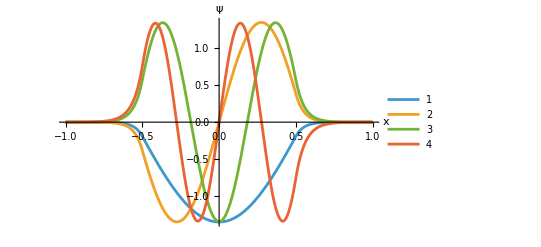

```mathematica
Plot[Evaluate[funsFinite], {x, -d, d}, PlotRange -> All,
   AxesLabel -> {"x", "ψ"}, PlotLegends -> Range[4]]
```

### Lab 2 — Rabi flopping, resonant and detuned

The lab drives a qubit and watches the excited-state population oscillate. Resonant driving fully inverts the qubit; detuning δ speeds the oscillation but caps its amplitude at 1/(1+δ^2). Read the population directly off the evolved state's amplitude (no formula assumed):

```mathematica
rabiP[δ_] := Abs[Normal[QuantumEvolve[
      (1/2) QuantumOperator["X"] + (δ/2) QuantumOperator["Z"],
      QuantumState["0"]]["StateVector"]][[2]]]^2;
{rabiP[0], rabiP[1]} // FullSimplify
```

{Abs[Sin[t/2]]^2,1/2 Abs[Sin[t/(√2)]]^2}

This returns {sin^2 (t/2),  1/2 sin^2 (t/√2)}: resonant flopping reaches 1, the detuned curve only 1/2. Plot the populations for three detunings:

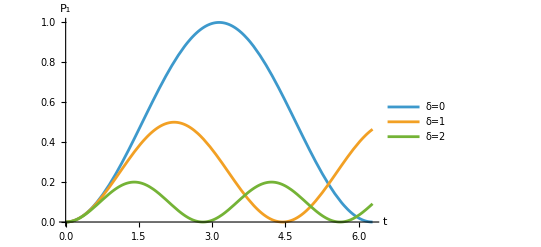

```mathematica
Plot[Evaluate[{rabiP[0], rabiP[1], rabiP[2]} /. t -> τ], {τ, 0, 2 Pi},
   AxesLabel -> {"t", "P₁"}, PlotLegends -> {"δ=0", "δ=1", "δ=2"}]
```

### Lab 3 — A logic circuit: the half-adder

The simplest classical arithmetic circuit adds two bits: the sum is their XOR (two CNOTs onto a target wire) and the carry is their AND (a Toffoli). Build it on four wires and read off the truth table by feeding each input and inspecting the output basis state:

```mathematica
ha = QuantumCircuitOperator[{"CNOT" -> {1, 3}, "CNOT" -> {2, 3}, "Toffoli" -> {1, 2, 4}}];
outBits[qs_] := IntegerDigits[First@First@Position[Round[Abs@Normal@qs["StateVector"]], 1] - 1, 2, 4];
Grid[Prepend[
   Flatten[Table[
      {a, b, Sequence @@ outBits[ha[QuantumState[StringJoin[ToString /@ {a, b, 0, 0}]]]][[3 ;; 4]]},
      {a, 0, 1}, {b, 0, 1}], 1],
   {"a", "b", "sum", "carry"}], Frame -> All]
```

a | b | sum | carry
0 | 0 | 0 | 0
0 | 1 | 1 | 0
1 | 0 | 1 | 0
1 | 1 | 0 | 1

The table reads 1 + 1 = 10 (sum 0, carry 1) and 1 + 0 = 01: a correct half-adder. Because every gate is reversible, the same circuit run on a superposition of inputs computes all four sums at once, which is the seed of quantum parallelism.

### Lab 4 — Magnetometry and the impact of noise

A Ramsey sequence turns an unknown field into a measurable phase: π/2 pulse, free precession at rate ω∝B for a time τ, second π/2 pulse, then read P_0. Dephasing during the free evolution shrinks the fringe contrast, which is the whole challenge of real magnetometry. Build the sequence with the field and the dephasing rate as inputs:

```mathematica
ramsey[ω_, γ_, τ_] := Module[{prep, free},
   prep = QuantumCircuitOperator[{"H" -> 1}][QuantumState["0"]];
   free = QuantumEvolve[(ω/2) QuantumOperator["Z"], {QuantumOperator["Z"]} -> {γ},
      prep, {t, 0, τ}];
   QuantumCircuitOperator[{"H" -> 1}][free[<|t -> τ|>]]["ProbabilitiesList"][[1]]];
Grid[Prepend[
   Table[{N[ω], ramsey[ω, 0, 2.] // Chop, ramsey[ω, 0.5, 2.] // Chop},
      {ω, 0, Pi, Pi/3}],
   {"ω", "P₀ ideal", "P₀ noisy"}], Frame -> All]
```

ω | P₀ ideal | P₀ noisy
0. | 1. | 0.567668
1.0472 | 0.25 | 0.466166
2.0944 | 0.25 | 0.466166
3.14159 | 1. | 0.567668

The ideal column swings over the full range [0,1] as the field changes; the noisy column (γ=0.5, τ=2) is squeezed toward 1/2 because the contrast has decayed by e^(-2γτ)≈0.14. A washed-out fringe carries less information about B: the sensor's precision is set by how long it can stay coherent, the same T_2 from Part 8.

Every code cell in this document was evaluated against QuantumFramework 2.0.0 before being written down; the numbers quoted are the framework's own output. Evaluate them yourself, then change the parameters and watch the physics respond.

Related Guides

Related Tech Notes

## Metadata

### Categorization

Tech Note

Wolfram`QuantumFramework`

### Keywords

quantum systems engineering

qubit

Rabi flopping

quantum harmonic oscillator

Jaynes-Cummings

teleportation

Lindblad

decoherence

quantum sensing

Ramsey

particle in a box